# Tree-level graviton scattering with FeynArts

Tree-level four-graviton scattering with FeynArts. The notebook works in three stages and gives every intermediate result a name, so any cell can be re-evaluated on its own.

First it builds the complete 2 → 2 tree amplitude off shell. FeynArts generates the three exchange diagrams and the four-graviton contact, the external polarisation tensors are attached as formal factorised tensors, and each diagram is contracted with FORM. The total is stored in theAmplitude[p1, p2, p3, p4].

Then it imposes the massless on-shell kinematics: FCClearScalarProducts[] removes earlier scalar-product assignments, SetMandelstam fixes the momentum products p_i·p_j, and a block of Pair assignments fixes the polarisation contractions, namely transversality of each wavefunction, the null property ε_i·ε_i=0, and the polarisation-momentum and polarisation-polarisation tables.

Finally it reduces the result to helicity amplitudes labelled by h_1,h_2,h_3,h_4=±1 and compares three combinations with closed forms in s, t and u.

Conventions: metric signature (+, -, -, -); FeynArts treats all external momenta as incoming, so the physical outgoing momenta p3 and p4 enter SetMandelstam as -p3 and -p4 and their polarisations carry the conjugated label -I. The gauge parameter is fixed at 2 by the model. No loop integration, spin sum or cross section is computed.

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the cell below with Shift+Enter. It loads FeynGrav, which loads FeynCalc and CalcFormConverter, and asks FeynCalc to load the installed patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. GenericModel is given explicitly because the classes file does not name its generic model and the FeynArts default is the stock "Lorentz" file. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
grModel="GR";
InitializeModel[grModel,GenericModel->grModel];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/GR/GR.gen

> $GenericMixing is OFF

generic model {GR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/GR/GR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {GR} initialized

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

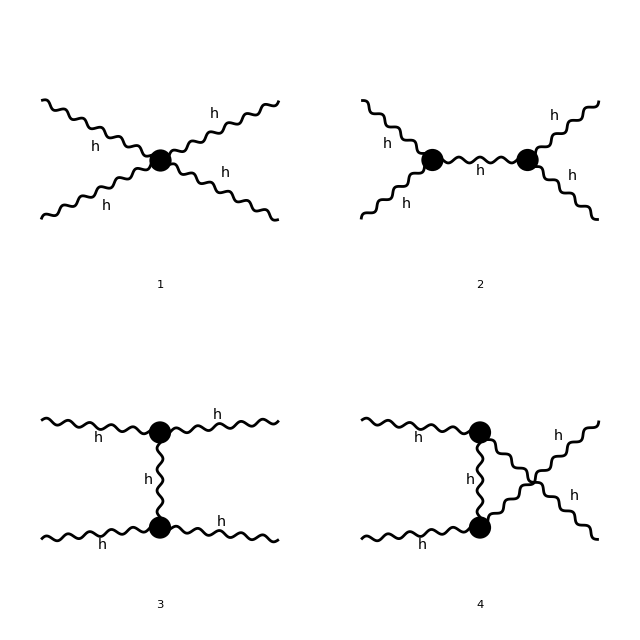

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 4. Form the total off-shell amplitude

Contract the diagrams separately with FORM to limit intermediate expression sizes. Each contraction uses CalcFormCalculate with its default options: the Lorentz dimension is inferred from the expression, which carries symbolic D, and successful FORM jobs are cleaned up automatically. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced.

The four contracted diagrams are summed immediately into theAmplitude[p1, p2, p3, p4]. The momenta are arguments of that definition, so a permuted evaluation, for instance the exchange of the two incoming legs, can be formed later from the same stored expression.

```mathematica
theAmplitude[p1_,p2_,p3_,p4_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;
```

theAmplitude[p1, p2, p3, p4] now holds the complete polarisation-contracted, amputated off-shell tree expression: all four diagrams with their graph factors, and still with unconstrained external virtualities, longitudinal contractions and trace terms.

Short shows only a preview and Length counts the terms of the stored expression; neither changes it. This is not yet an on-shell scattering amplitude, and it contains no loop measure or spin sum.

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D (p1·ε(p2)) (p2·ε(p1)) (p3·«1») (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

## 5. On-shell amplitude

Everything above is off shell: the p_i^2 and the polarisation contractions are still free. This section fixes them in three steps, clearing the old scalar products, fixing the momenta and fixing the polarisations, and then reduces the result to helicity amplitudes.

The Pair assignments below are global. The final FCClearScalarProducts[] cell removes these assignments and the Mandelstam scalar-product settings, so the stored off-shell expression can be used again. Re-evaluate the on-shell setup before repeating the helicity reduction. This cleanup does not reset $Assumptions or erase the stored amplitude definitions.

FCClearScalarProducts[] removes any scalar-product assignments made earlier in the session, so the on-shell relations that follow are applied to a clean state rather than on top of stale values.

```mathematica
FCClearScalarProducts[]
```

SetMandelstam fixes the momentum products p_i·p_j for massless momenta. The physical outgoing momenta p3 and p4 are passed as -p3 and -p4 because SetMandelstam works with all-incoming momenta, and the four mass arguments are zero. This sets p_1·p_2=p_3·p_4=s/2, p_1·p_3=p_2·p_4=-t/2, and p_1·p_4=p_2·p_3=-u/2, which implies s + t + u = 0 together with t=-2 E^2(1-cosθ) and u=-2E^2(1+cosθ) in the centre-of-mass frame. Nothing is said yet about the polarisations.

```mathematica
SetMandelstam[s, t, u, p1 , p2 , -p3 , -p4 , 0 , 0 , 0 , 0 ];
```

Transversality: each wavefunction is orthogonal to its own momentum, ε_i,p_i=0. The momentum is the physical one, so this holds for the incoming legs 1 and 2 and for the conjugated outgoing legs 3 and 4.

```mathematica
Pair[Momentum[p1,D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[p2,D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[p3,D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[p4,D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

Null wavefunctions: ε_i·ε_i=0 in the bilinear product. This is a statement about each leg on its own; the products between different legs are fixed by the two blocks that follow.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

The mixed products that vanish: ε_1·p_2, ε_2·p_1, ε_3·p_4, and ε_4·p_3 are zero. Each wavefunction has zero time component, so these reduce to spatial scalar products, which vanish for the leg pairings shown.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p2,D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p1,D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p4,D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p3,D]]=0;
```

The polarisation-momentum products. With h_i=±1 the whole block equals ⅈ √((t u)/(2 s)) times a matrix built from the helicity labels; it is written out leg by leg here. The products are bilinear, with no complex conjugation, and the momenta are the physical ones.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p3,D]]=-h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p4,D]]=h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p3,D]]=h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p4,D]]=-h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p1,D]]=-h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p2,D]]=h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p1,D]]=h4 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p2,D]]=-h4 ⅈ/Sqrt[2] Sqrt[t u/s];
```

The polarisation-polarisation products, again bilinear with no conjugation. The diagonal is zero because each wavefunction is null. Off the diagonal the entries carry the helicity labels of the two legs together with the ratio t/s; using 1+2 t/s=cosθ they encode the helicity correlations that the final amplitudes are built from.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=-(1+h1 h2)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=-(h1 h3 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=(h1 h4 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=(h2 h3 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(h2 h4 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(1+h3 h4)/2;
```

Simplify needs to know that the helicity labels are ±1 before it can collapse the polynomials in h_i introduced by the tables above.

```mathematica
$Assumptions=h1^2==h2^2==h3^2==h4^2==1;
```

This is where the off-shell expression becomes a helicity amplitude. theAmplitude already depends on s, t and u through the assignments above; Simplify applies the h_i^2=1 assumptions and TrickMandelstam rewrites the result in the standard variables, storing it in theAmplitudeonShell, again as a function of the four helicity labels.

```mathematica
theAmplitudeonShell[h1_,h2_,h3_,h4_]=TrickMandelstam[theAmplitude[p1,p2,p3,p4]//Simplify,{s,t,u,0}];//Timing
```

{1.42878,Null}

Check against closed forms. Each of the three helicity combinations is compared with the expected tree-level expression. Both sides are put in s, t and u by TrickMandelstam before the comparison. The recorded outputs are True for each combination.

```mathematica
TrickMandelstam[theAmplitudeonShell[+1,+1,+1,+1],{s,t,u,0}]==ⅈ κ^2/4 s^4/(s t u)
TrickMandelstam[theAmplitudeonShell[+1,-1,-1,+1],{s,t,u,0}]==ⅈ κ^2/4 t^4/(s t u)
TrickMandelstam[theAmplitudeonShell[+1,-1,+1,-1],{s,t,u,0}]==ⅈ κ^2/4 u^4/(s t u)
```

True

True

True

Scope of the result. This is the massless tree-level four-graviton amplitude, evaluated with the gauge parameter fixed at 2 by the model, using the polarisation conventions fixed above; h_i=±1 are the helicity labels. No loop integration, ultraviolet subtraction, spin sum, phase-space integration or cross section is computed, and the off-shell expression from the earlier sections remains available in theAmplitude until the kernel is restarted.

```mathematica
FCClearScalarProducts[]
```